```mathematica
SetOptions[EvaluationNotebook[],AutoGeneratedPackage->"FEDeriK.m"]
```

## Global variables

```mathematica
ModuleLoaded::dependency="The module `1` requires `2`, which has not been loaded.";

If[ModuleLoaded[FunKit]=!=True,
Message[ModuleLoaded::dependency,"FEDeriK","FunKit"];
Abort[];
];

ModuleLoaded[FEDeriK]=True;
```

```mathematica
$userCorrelationFunctions={};
$userIndexedObjects={};

$CorrelationFunctions:={Propagator,GammaN}∪$userCorrelationFunctions;
$OrderedObjects:=$CorrelationFunctions∪{Rdot};
$indexedObjects:=$OrderedObjects∪{ABasis,VBasis,γ}∪$userIndexedObjects;
$allObjects:={FMinus}∪$indexedObjects

$MaxDerivativeIterations=500;
$CanonicalOrdering="f>af>b";
```

```mathematica
AddIndexedObject[name_Symbol]:=Module[{},
AppendTo[$userIndexedObjects,name];
$userIndexedObjects=DeleteDuplicates[$userIndexedObjects];
];
```

```mathematica
$FunKitDirectory=SelectFirst[Join[{FileNameJoin[{$UserBaseDirectory,"Applications","FunKit"}],FileNameJoin[{$BaseDirectory,"Applications","FunKit"}],FileNameJoin[{$InstallationDirectory,"AddOns","Applications","FunKit"}],FileNameJoin[{$InstallationDirectory,"AddOns","Packages","FunKit"}],FileNameJoin[{$InstallationDirectory,"AddOns","ExtraPackages","FunKit"}]},Select[$Path,StringContainsQ[#,"FunKit"]&]],DirectoryQ[#]&]<>"/";
```

```mathematica
WetterichEquation:=Module[{a,b},
FEq[FTerm[Propagator[{AnyField,AnyField},{a,b}],Rdot[{AnyField,AnyField},{-a,-b}]/2]]
];
```

## FDOp, FTerm and FEq definitions

### Basic definitions

```mathematica
Unprotect[FTerm];
ClearAll[FTerm];

FTimesPowerPatternaToFTermb=Power[a,FTerm[b_]];
FTimesPowerPatternFTermbtoa=Power[a,FTerm[b_]];

FTerm::TimesError="An FTerm cannot be multiplied using Times[__]. To multiply FTerms, use term1**term2, also with scalars, a**term. Error in expression
`1`";
FTerm::FTermPowerError="An FTerm cannot be taken to a power of an FTerm.";

(*Multiplication of FTerms*)
FTerm/:NonCommutativeMultiply[FTerm[a__],FTerm[b__]]:=FTerm[a,b]
FTerm[pre___,NonCommutativeMultiply[in___],post___]:=FTerm[pre,in,post]
FTerm[pre___,Times[inpre__,NonCommutativeMultiply[in___],inpost__],post___]:=FTerm[pre,inpre*inpost,in,post]
FTerm[first_,pre___,Times[a_,other2_],post___]/;NumericQ[first]&&NumericQ[a]&&Head[first]=!=FDOp:=FTerm[first*a,pre,other2,post]
FTerm[first_,pre___,Times[a_,other2_],post___]/;Not[NumericQ[first]]&&NumericQ[a]&&Head[first]=!=FDOp:=FTerm[a,first,pre,other2,post]
FTerm[first_,pre___,a_,post___]/;NumericQ[first]&&NumericQ[a]:=FTerm[first*a,pre,post]
FTerm[first_,pre___,a_,post___]/;Not[NumericQ[first]]&&NumericQ[a]:=FTerm[a,first,pre,post]
FTerm[]:=FTerm[1]

(*Pre-reduction of zero FTerms*)
FTerm[___,0,___]:=FTerm[0]

(*Reduction of immediately nested FTerms*)
FTerm[pre___,FTerm[in__],post___]:=FTerm[pre,in,post] 

FTerm/:Power[FTerm[a___],FTerm[b___]]:=(Message[FTerm::FTermPowerError];Abort[]);

Protect[FTerm];
```

```mathematica
Unprotect[FEq];
ClearAll[FEq];

FEq::TimesError="A FEq cannot be multiplied using Times[__]. To multiply FEqs, use eq1**eq2, also with scalars, a**eq. Error in expression
`1`";

(*Removal of zero FTerms*)
FEq[pre___,FTerm[___,0,___],post___]:=FEq[pre,post]

(*Sum splitting of FTerms*)
FEq[preEq___,FTerm[preTerm___,Plus[a_,b__],postTerm___],postEq___]:=FEq[preEq,FTerm[preTerm,a,postTerm],FTerm[preTerm,Plus[b],postTerm],postEq]

(*Sums of FTerms*)
FEq[preEq___,Plus[FTerm[a__],FTerm[b__],c___],postEq___]:=FEq[preEq,FTerm[a],Plus[FTerm[b],c],postEq]
FEq/:Plus[FEq[a___],FTerm[b__]]:=FEq[a,FTerm[b]]

(*Sums of FEqs*)
FEq/:Plus[preEq___,FEq[terms1___],midEq___,FEq[terms2___],postEq___]:=Plus[preEq,midEq,postEq,FEq[terms1,terms2]]

(*Multiplication of FEqs*)
FEq/:Times[pre___,FEq[a__],post___]:=(Message[FEq::TimesError,{pre,FEq[a],post}];Abort[])
FEq[prefeq__,Times[pre___,FTerm[a__],post___],postfeq__]:=(Message[FTerm::TimesError,{pre,FTerm[a],post}];Abort[])

FEq/:NonCommutativeMultiply[FTerm[b__],FEq[c__]]:=FEq[Map[FTerm[b]**#&,FEq[c]]]
FEq/:NonCommutativeMultiply[FEq[a__],FEq[b__]]:=FEq@@(Flatten@Table[FEq[{a}[[i]]**{b}[[j]]],{i,1,Length[{a}]},{j,1,Length[{b}]}])
FEq/:NonCommutativeMultiply[FTerm[b___],FEq[]]:=FEq[]
FEq/:NonCommutativeMultiply[FTerm[],FEq[b___]]:=FEq[]
FEq/:NonCommutativeMultiply[FTerm[0],FEq[b___]]:=FEq[]
FEq/:FTerm[FEq[a__]]:=FEq[a];
FEq/:FTerm[FEq[a__],FEq[b__]]:=FEq@@(Flatten@Table[FEq[{a}[[i]]**{b}[[j]]],{i,1,Length[{a}]},{j,1,Length[{b}]}])

(*Reduction of immediately nested FEqs*)
FEq[pre___,FEq[in___],post___]:=FEq[pre,in,post]

Protect[FEq];
```

### Checks and assertions

#### FTerm and FEq

```mathematica
FTermQ[expr_]:=Head[expr]===FTerm;
FTerm::notFTerm="The term `1` is not an FTerm.";
AssertFTerm[expr_]:=If[Not@FTermQ[expr],Message[FTerm::notFTerm,expr];Abort[]];

FEqQ[expr_]:=Head[expr]===FEq;
FEq::notFEq="The term `1` is not an FEq.";
AssertFEq[expr_]:=If[Not@FEqQ[expr],Message[FEq::notFEq,expr];Abort[]];
```

#### FMinus

```mathematica
Unprotect[FMinus];
ClearAll[FMinus];

(*Grassmann minus signs do not care about index positioning. We force them always up*)
FMinus[{a_,b_},{Times[-1,ia_],ib_}]:=FMinus[{a,b},{ia,ib}]
FMinus[{a_,b_},{ia_,Times[-1,ib_]}]:=FMinus[{a,b},{ia,ib}]

(*Powers are simple*)
FMinus/:Power[FMinus[{a_,b_},{ia_,ib_}],n_Integer]/;EvenQ[n]:=1
FMinus/:Power[FMinus[{a_,b_},{ia_,ib_}],n_Integer]/;OddQ[n]:=FMinus[{a,b},{ia,ib}]

Protect[FMinus];
```

#### Field Space

```mathematica
(* Check if a given field definition is valid. Can be either its own anti-field or a pair {af,f} *)
FieldDefQ[expr_]:=Module[{},
If[Head[expr]===List,
If[Length[expr]=!=2,
Print["A field definition must be either of form f[x...] or {af[x...],f[x...]}. \"",expr,"\" does not fit."];Return[False]];

If[Head[expr[[1]]]===Head[expr[[2]]],
Print["A field definition {af[x...],f[x...]} must have different field names af and f. \"",expr,"\" does not fit."];
Return[False]];

If[Not@(List@@(expr[[1]])===List@@(expr[[2]])),
Print["A field definition {af[x...],f[x...]} must have identical indices. \"",expr,"\" does not fit."];
Return[False]];

Do[
If[Not@(MatchQ[expr[[i]],_Symbol[_,{__Symbol}]]||MatchQ[expr[[i]],_Symbol[_]]),
Print["A field definition f[x...] must have indices f[p] or f[p,{a,b,...}]. \"",expr[[i]],"\" does not fit."];
Return[False]],
{i,1,2}
];

Return[True];
];

If[Not@(MatchQ[expr,_Symbol[_,{__Symbol}]]||MatchQ[expr,_Symbol[_]]),
Print["A field definition f[x...] must have indices f[p] or f[p,{a,b,...}]. \"",expr,"\" does not fit."];
Return[False]];

Return[True];
];

FieldDef::invalidFieldDefinition="The given field definition `1` is not valid.";

AssertFieldDef[expr_]:=If[Not@FieldDefQ[expr],
Message[FieldDefinition::invalidFieldDefinition];
Abort[]];
```

```mathematica
(* Check if a given field space definition is valid *)
FieldSpaceDefQ[fieldSpace_]:=Module[{},
If[Head[fieldSpace]=!=Association,Print["An FSetup must be an association"];Return[False]];

If[Not@(Keys[fieldSpace]==={"cField","Grassmann"}),
Print["fields must contain the two keys {\"cField\",\"Grassmann\"}!"];
Return[False]];

If[Not@ListQ[fieldSpace["cField"]],
Print["fields[\"cField\"] must be a list!"];
Return[False]];

If[Not@(And@@Map[FieldDefQ,fieldSpace["cField"]]),
Print["fields[\"cField\"] must contain valid fields!"];
Return[False]];

If[Not@ListQ[fieldSpace["Grassmann"]],
Print["fields[\"Grassmann\"] must be a list!"];
Return[False]];

If[Not@(And@@Map[FieldDefQ,fieldSpace["Grassmann"]]),
Print["fields[\"Grassmann\"] must contain valid fields!"];
Return[False]];

Return[True];
];

FieldSpaceDefinition::invalidFieldDefinition="The given field space definition is invalid.";

AssertFieldSpaceDef[fields_]:=If[Not@FieldSpaceDefQ[fields],
Message[FieldSpaceDefinition::invalidFieldDefinition];Abort[]];
```

#### FSetup

```mathematica
FSetup::notFSetup="The given setup is not valid!";

FSetupQ[setup_]:=Module[{},
If[Not@(Head[setup]===Association),
Print["A valid setup must be an Association!"];
Return[False]];

If[Not@MemberQ[Keys[setup],"FieldSpace"],
Print["A valid setup must have the key \"FieldSpace\"!"];
Return[False]];

If[Not@FieldSpaceDefQ[setup["FieldSpace"]],
Return[False]];

Return[True];
];

AssertFSetup[setup_]:=Module[{},
If[Not@(Head[setup]===Association),
Print["A valid setup must be an Association!"];
Message[FSetup::notFSetup];
Abort[]];

If[Not@MemberQ[Keys[setup],"FieldSpace"],
Print["A valid setup must have the key \"FieldSpace\"!"];
Message[FSetup::notFSetup];
Abort[]];

AssertFieldSpaceDef[setup["FieldSpace"]];
];
```

#### Existence of a field

```mathematica
(* Check if a given field definition is valid. Can be either its own anti-field or a pair {af,f} *)
FieldQ[setup_,expr_]:=Module[{},
If[Not@(MatchQ[expr,_Symbol[_,{__Symbol}]]||MatchQ[expr,_Symbol[_]]),
Print["A field f[x...] must have indices f[p] or f[p,{a,b,...}]. \"",expr,"\" does not fit."];
Return[False]];

If[Not@(MemberQ[Map[Head,setup["FieldSpace"]//Values//Flatten],Head[expr]]),
Print["The field \"",expr,"\" is not contained in the field space."];
Return[False]];

Return[True];
];

Field::invalidField="The given field `1` does not exist.";

AssertField[setup_,expr_]:=If[Not@FieldQ[setup,expr],
Message[FieldDefinition::invalidField];
Abort[]];
```

#### Derivative List

```mathematica
(*Check a derivative list for correct formatting.*)
DerivativeListQ[setup_,derivativeList_]:=Module[{},

If[Not@(Head[derivativeList]===List),
Print["A valid derivativeList must be an List!"];
Return[False]];

If[Not@AllTrue[derivativeList,FieldQ[setup,#]&],
Print["A valid derivativeList must be an List of fields f_[p_,{___}] of f_[p_] which have been defined in the setup!"];
Return[False]];

Return[True];
];

DeriveEquation::invalidDerivativeList="The given derivativeList `1` is not valid.";

AssertDerivativeList[setup_,expr_]:=If[Not@DerivativeListQ[setup,expr],
Message[DeriveEquation::invalidDerivativeList];
Abort[]];
```

#### FDOp

```mathematica
Unprotect[FDOp];
ClearAll[FDOp];

FDOp::invalid="`1` is not a valid FDOp.";
FDOp::invalidArguments="`1` is not a valid FDOp. FDOp takes a single field with an index as argument.";
FDOp::arithmetic="An FDOp cannot be included as anything but a factor in an FTerm. Error in 
  `1`";

FDOp/:Times[a___,FDOp[b___],c___]:=(Message[FDOp::arithmetic,StringTake[ToString@(Hold@Times[a,FDOp[b],c]),{6,-2}]];Abort[])
FDOp/:Plus[a___,FDOp[b___],c___]:=(Message[FDOp::arithmetic,StringTake[ToString@(Hold@Plus[a,FDOp[b],c]),{6,-2}]];Abort[])

FDOp[a_,b__]:=(Message[FDOp::invalidArguments,StringTake[ToString@(Hold@FDOp[a,b]),{6,-2}]];Abort[])

FDOpQ[setup_,expr_]:=(Head[expr]===FDOp)&&MatchQ[expr,(_[_,{__}]|_[_])]&&FieldQ[setup,#]&@@expr;
AssertFDOp[setup_,expr_]:=If[Not@FDOpQ[setup,expr],Message[FDOp::invalid,expr];Abort[]];

Protect[FDOp];
```

## Utilities

```mathematica
Protect[GammaN,Propagator,AnyField,ABasis,VBasis,FieldIndices];
```

#### Getting symbols

```mathematica
exclusions[a_]:=And@@{a=!=List,a=!=Complex,a=!=Plus,a=!=Power,a=!=Times}
GetAllSymbols[expr_]:=DeleteDuplicates@Cases[
Flatten[{expr}//.Times[a_,b__]:>{a,b}//.a_Symbol[b__]/;exclusions[a]:>{a,b}],
_Symbol,
Infinity]
```

### FunctionalD

```mathematica
FunctionalD::malformed="Cannot take a derivative of `1`. Expression is either malformed or this is a bug.";

ClearAll[FunctionalD]
FunctionalD[expr_,v:(f_[_]|{f_[_],_Integer})..,OptionsPattern[]]:=Internal`InheritedBlock[
{f,GammaN,Propagator,nonConst,FTerm,FEq},

nonConst=Sort@{f,GammaN,Propagator,Power};

Unprotect[GammaN,Propagator,FTerm,FEq,AnyField];

(*Rule for normal functional derivatives*)
f/:D[f[x_],f[y_],NonConstants->nonConst]:=γ[{f,f},{-y,x}];
(*Ignore fields without indices. These are usually tags*)
f/:D[f,f[y_],NonConstants->nonConst]:=0;(*δ[#,y]&;*)

(*Derivative rule for GammaN*)
GammaN/:D[GammaN[{a__},{b__}],f[if_],NonConstants->nonConst]:=GammaN[{f,a},{-if,b}];

(*Derivative rule for Propagators*)
Propagator/:D[Propagator[{b_,a_},{ib_,ia_}],f[if_],NonConstants->nonConst]:=Module[
{ic,id,ie,ig},
((-1)FMinus[{a,a},{id,id}]FMinus[{f,b},{if,ib}])**
Propagator[{b,AnyField},{ib,ic}]**
GammaN[{AnyField,f,AnyField},{-ic,-if,-id}]**
Propagator[{AnyField,a},{id,ia}]
];

(*No derivatives of FTerm, FEq*)
FTerm/:D[FTerm[a___],f[y_],NonConstants->nonConst]:=(Message[FunctionalD::malformed,FTerm[a]];Abort[]);
FEq/:D[FEq[a___],f[y_],NonConstants->nonConst]:=(Message[FunctionalD::malformed,FEq[a]];Abort[]);

(*Chain rules*)
f/:D[g_[FTerm[a___]],f[y_],NonConstants->nonConst]:=(FTerm[g'[FTerm[a]]]**FTerm[FDOp[f[y]],a]);
f/:D[Power[FTerm[a___],b_],f[y_],NonConstants->nonConst]:=(FTerm[b,Power[FTerm[a],b-1]]**FTerm[FDOp[f[y]],a]);
f/:D[Power[a_,FTerm[b___]],f[y_],NonConstants->nonConst]:=(FTerm[Log[a],Power[a,FTerm[b]]]**FTerm[FDOp[f[y]],b]);

Protect[GammaN,Propagator,FTerm,FEq,AnyField];

D[expr,v,NonConstants->nonConst]
];

FunctionalD::badArgumentFTerm="Cannot take derivative of an FTerm. Use TakeDerivatives instead.";
FunctionalD[FTerm[expr_],v:(f_[_]|{f_[_],_Integer})..,OptionsPattern[]]:=(Message[FunctionalD::badArgumentFTerm];Abort[]);

FunctionalD::badArgumentFEq="Cannot take derivative of an FEq. Use TakeDerivatives instead.";
FunctionalD[FEq[___],v:(f_[_]|{f_[_],_Integer})..,OptionsPattern[]]:=(Message[FunctionalD::badArgumentFEq];Abort[]);
```

### Field and index information

#### Fields

```mathematica
GetcFields[setup_]:=Map[
If[Head[#]===List,Head[#[[2]]],Head[#]]&,
setup["FieldSpace"]["cField"]
];
GetAnticFields[setup_]:=Select[Map[
If[Head[#]===List,Head[#[[1]]],{}]&,
setup["FieldSpace"]["cField"]
],#=!={}&];

GetGrassmanns[setup_]:=Map[
If[Head[#]===List,Head[#[[2]]],Head[#]]&,
setup["FieldSpace"]["Grassmann"]
];
GetAntiGrassmanns[setup_]:=Select[Map[
If[Head[#]===List,Head[#[[1]]],{}]&,
setup["FieldSpace"]["Grassmann"]
],#=!={}&];


GetCommuting[setup_]:=Flatten@Select[Map[
If[Head[#]===List,{Head[#[[1]]],Head[#[[2]]]},Head[#]]&,
setup["FieldSpace"]["cField"]
],#=!={}&];

GetAntiCommuting[setup_]:=Flatten@Select[Map[
If[Head[#]===List,{Head[#[[1]]],Head[#[[2]]]},Head[#]]&,
setup["FieldSpace"]["Grassmann"]
],#=!={}&];
```

```mathematica
GetFieldPairs[setup_]:=Map[{Head[#[[1]]],Head[#[[2]]]}&,
Select[
Join[setup["FieldSpace"]["Grassmann"],setup["FieldSpace"]["cField"]],
Head[#]===List&
]
];

GetSingleFields[setup_]:=Map[Head[#]&,Select[
Join[setup["FieldSpace"]["Grassmann"],setup["FieldSpace"]["cField"]],
Head[#]=!=List&
]
];

GetAllFields[setup_]:=Join[Flatten@GetFieldPairs[setup],GetSingleFields[setup]];

HasPartnerField[setup_,field_]:=MemberQ[
Flatten@GetFieldPairs[setup],
field
];
HasPartnerField[setup_,field_[__]]:=HasPartnerField[setup,field];

IsGrassmann[setup_,field_]:=MemberQ[GetGrassmanns[setup],field];
IsGrassmann[setup_,field_[__]]:=IsGrassmann[setup,field];

IsAntiGrassmann[setup_,field_]:=MemberQ[GetAntiGrassmanns[setup],field];
IsAntiGrassmann[setup_,field_[__]]:=IsAntiGrassmann[setup,field];

IscField[setup_,field_]:=MemberQ[GetcFields[setup],field];
IscField[setup_,field_[__]]:=IscField[setup,field];

IsAnticField[setup_,field_]:=MemberQ[GetAnticFields[setup],field];
IsAnticField[setup_,field_[__]]:=IsAnticField[setup,field];
```

```mathematica
GetPartnerField[setup_,field_Symbol]:=Module[{pairs,sel},
If[Not@HasPartnerField[setup,field],Return[field]];

pairs=GetFieldPairs[setup];

sel=Select[pairs,MemberQ[#,field,Infinity]&][[1]];
sel=DeleteCases[sel,field];
If[Length[sel]>0,Return[sel[[1]]]];

Print["field ",field," not found!"];Abort[];
];
GetPartnerField[setup_,field_Symbol[i__]]:=GetPartnerField[setup,field][i]
```

#### Checking field content of expressions

```mathematica
ExtractFields[setup_Association,expr_]:=Module[{},
Return@(DeleteDuplicates[Head/@Cases[{expr},
Alternatives@@Map[Blank,GetAllFields[setup]],
Infinity
]]);
];
ExtractFieldsWithIndex[setup_Association,expr_]:=Module[{},
Return@Cases[{expr},
Alternatives@@Map[Blank,GetAllFields[setup]],
Infinity
];
];
```

```mathematica
ContainsGrassmann[setup_Association,expr_]:=Module[{},
Return@
AnyTrue[ExtractFields[setup,expr],IsGrassmann[setup,#]||IsAntiGrassmann[setup,#]&];
]
GrassmannCount[setup_Association,expr_]:=Module[{},
Return[Length@
Select[ExtractFieldsWithIndex[setup,expr],IsGrassmann[setup,Head[#]]||IsAntiGrassmann[setup,Head[#]]&]
];
]
```

#### Indices

```mathematica
(*Get a list of all unique super-indices within the expression expr*)
GetAllSuperIndices[setup_,expr_FTerm]:=Module[{idxO,idxF},
idxO=Cases[expr,
Alternatives@@(Map[Blank[#]&,$indexedObjects]),
{1,3}];
idxF=Cases[expr,
Alternatives@@(Map[Blank[#]&,GetAllFields[setup]]),
{1,3}];
Return[(idxF[[All,1]]∪Flatten[idxO[[All,2]]]/.Times[_,a_Symbol]:>a//DeleteDuplicates)]
];
GetAllSuperIndices[setup_Association,expr_FEq]:=Module[{},
Return@(GetAllSuperIndices[setup,#]&/@(List@@expr))
];
```

```mathematica
ExtractObjectsWithIndex[setup_Association,expr_FTerm]:=Module[{},
Return@Cases[expr,
Alternatives@@(Map[Blank[#]&,$indexedObjects∪GetAllFields[setup]]),
{1,3}];
];
ExtractObjectsWithIndex[setup_Association,expr_FEq]:=Module[{},
Return@(
(ExtractObjectsWithIndex[setup,#]&/@(List@@expr))
)
];
```

```mathematica
ExtractObjectsAndIndices[setup_,expr_FTerm]:=Module[{idxO,idxF},
idxO=Cases[expr,
Alternatives@@(Map[Blank[#]&,$indexedObjects]),
{1,3}];
idxF=Cases[expr,
Alternatives@@(Map[Blank[#]&,GetAllFields[setup]]),
{1,3}];
Return[{idxO∪idxF,
(idxF[[All,1]]∪Flatten[idxO[[All,2]]]/.Times[_,a_Symbol]:>a//DeleteDuplicates)}]
];
ExtractObjectsAndIndices[setup_Association,expr_FEq]:=Module[{},
Return@({Flatten[#[[All,1]]],Flatten[#[[All,2]]]}&@
(ExtractObjectsAndIndices[setup,#]&/@(List@@expr))
)
];
```

```mathematica
SuperIndices::undeterminedSums="There are indices with count > 2 in the expression
    `1`
This is not allowed for valid terms/equation. Problematic indices:
    `2`";
```

```mathematica
(*Get a list of all closed super-indices within the expression expr*)
GetClosedSuperIndices[setup_,expr_]:=Module[{objects,indices,count},
{objects,indices}=ExtractObjectsAndIndices[setup,expr];

count=Map[Count[objects,#,Infinity]&,indices];
If[AnyTrue[count,#>2&],Message[SuperIndices::undeterminedSums,expr,Pick[indices,#>2&/@count]];Abort[]];

Return[
Pick[indices,
Map[Mod[#,2]===0&,count]
]
];
];
```

```mathematica
(*Get a list of all open super-indices within the expression expr*)
GetOpenSuperIndices[setup_,expr_]:=Module[{objects,indices,count},
{objects,indices}=ExtractObjectsAndIndices[setup,expr];

count=Map[Count[objects,#,Infinity]&,indices];
If[AnyTrue[count,#>2&],Message[SuperIndices::undeterminedSums,expr,Pick[indices,#>2&/@count]];Abort[]];

Return[
Pick[indices,
Map[Mod[#,2]=!=0&,count]
]
];
];
```

```mathematica
(*Check whether all indices are closed within expr. 
This disallows also multiple use of a single index name, !anywhere!*)
AllIndicesClosed[setup_,expr_]:=Module[{objects,indices,count},
{objects,indices}=ExtractObjectsAndIndices[setup,expr];

count=Map[Count[objects,#,Infinity]&,indices];
Return[AllTrue[count,#==2&]];
];

SuperIndicesValid[setup_,expr_]:=Module[{objects,indices,count},
{objects,indices}=ExtractObjectsAndIndices[setup,expr];

count=Map[Count[objects,#,Infinity]&,indices];
If[AnyTrue[count,#>2&],Message[SuperIndices::undeterminedSums,expr,Pick[indices,#>2&/@count]];Return[False]];

Return[True];
];
```

### Ordering

#### Setting the canonical ordering

```mathematica
$AvailableCanonicalOrderings={"f>af>b","af>f>b","b>f>af","b>af>f"};

CanonicalOrdering::unknownInteger="The integer `1` should be between 1 and 4.";
CanonicalOrdering::unknownString="The expression `1` should be one of "<>ToString[$AvailableCanonicalOrderings];

SetCanonicalOrdering[a_Integer]:=Module[{},
Switch[a,
1,$CanonicalOrdering="f>af>b",

2,$CanonicalOrdering="af>f>b",

3,$CanonicalOrdering="b>f>af",

4,$CanonicalOrdering="b>af>f",

_,Message[CanonicalOrdering::unknownInteger,a]
];
Print["Canonical ordering set to ",$CanonicalOrdering];
];

SetCanonicalOrdering[a_]:=Module[{},
Switch[a,
"f>af>b",$CanonicalOrdering="f>af>b",

"af>f>b",$CanonicalOrdering="af>f>b",

"b>f>af",$CanonicalOrdering="b>f>af",

"b>af>f",$CanonicalOrdering="b>af>f",

_,Message[CanonicalOrdering::unknownString,a]
];
Print["Canonical ordering set to ",$CanonicalOrdering];
];
```

#### Ordering expressions

```mathematica
(*Returns true if f1 < f2, and false if f1 > f2*)
FieldOrderLess[setup_,f1_Symbol,f2_Symbol]:=Module[
{kind1,kind2,
idxOrder,
n1,n2},

kind1={IsGrassmann[setup,#],IsAntiGrassmann[setup,#],IscField[setup,#],IsAnticField[setup,#],#===AnyField}&[f1];
kind2={IsGrassmann[setup,#],IsAntiGrassmann[setup,#],IscField[setup,#],IsAnticField[setup,#],#===AnyField}&[f2];

Switch[$CanonicalOrdering,
"f>af>b",
idxOrder={4,3,2,1,0},
"af>f>b",
idxOrder={3,4,1,2,0},
"b>f>af",
idxOrder={2,1,4,3,0},
"b>af>f",
idxOrder={1,2,3,4,0},
_,
Print["Order failure: order \""<>$CanonicalOrdering<>"\" unknown."];Abort[];
];

n1=Pick[idxOrder,kind1][[1]];
n2=Pick[idxOrder,kind2][[1]];

Return[n1<n2]
];
```

```mathematica
(*Returns the sign that results from exchanging the two fields f1 and f2*)
CommuteSign[setup_,f1_,f2_]:=Module[{},
Return[
-2*Boole[MemberQ[GetAntiCommuting[setup],f1]&&MemberQ[GetAntiCommuting[setup],f2]]+1
];
];
```

```mathematica
(*Find all instances of $OrderedObjects and order their field value according to the canonical scheme*)
OrderObject[setup_,expr_]:=expr;
OrderObject[setup_,obj_[fields_List,indices_List]/;MemberQ[$OrderedObjects,obj]]:=Module[
{i,j,curi,prefactor,pref,reverse,
nfields=fields,nindices=indices,
trackedField},

(*Do not order if there is an undetermined field!*)
If[MemberQ[nfields,AnyField]||FreeQ[$indexedObjects,obj],Return[obj[nfields,nindices]]];

(*The propagator gets a reverse ordering*)
reverse=If[obj===Propagator,True,False];
pref=If[reverse,Identity,Not];
prefactor=1;

(*Always compare the ith field with all previous fields and put it in the right place.
Iterate until one reaches the end of the array, then it is sorted.*)
For[i=1,i<=Length[nfields],i++,
curi=i;
(*Check if we should switch curi and curi-1*)
While[curi>=2&&pref@FieldOrderLess[setup,nfields[[curi]],nfields[[curi-1]]],
nfields[[{curi,curi-1}]]=nfields[[{curi-1,curi}]];
nindices[[{curi,curi-1}]]=nindices[[{curi-1,curi}]];
prefactor*=CommuteSign[setup,nfields[[curi]],nfields[[curi-1]]];
curi--;
];
];

Return[prefactor*obj[nfields,nindices]];
];
OrderFields[setup_,expr_]:=Map[OrderObject[setup,#]&,expr,Infinity];
```

### QMeS Compatibility

```mathematica
(*Compatibility: Output any expression in a Form which looks like QMeS output*)
QMeSNaming[setup_,expr_]:=expr;
QMeSNaming[setup_,obj_[fields_List,indices_List]/;MemberQ[$OrderedObjects,obj]]:=Module[
{oldCanonicalOrdering,transf,prefactor,
mobj,mfields,mindices,
prefix,fieldPart,indexPart},

(*QMeS follows b>af>f, so we switch temporarily!*)
Block[{$CanonicalOrdering},
$CanonicalOrdering="b>af>f";
transf=OrderObject[setup,obj[fields,indices]];
];

prefactor=1;
If[MatchQ[transf,Times[-1,a_]],prefactor=-1;transf=-transf;];
mobj=Head[transf];
mfields=(List@@transf)[[1]];
mindices=(List@@transf)[[2]];

prefix=Switch[obj,
Propagator,"G",
GammaN,"Γ",
Rdot,"Rdot"
];
fieldPart=StringJoin[Map[ToString,mfields]];
indexPart=Flatten[mindices];
Return[prefactor*Symbol[prefix<>fieldPart][indexPart]];
];
QMeSForm[setup_,expr_]:=Map[QMeSNaming[setup,#]&,expr,{1,3}]//.{FEq:>List,FTerm:>List};
```

### Reduce metric factors

```mathematica
(*Is an index down?*)
isNeg[i_]:=MatchQ[i,Times[-1,a_Symbol]];
makePosIdx[i_]:=If[isNeg[i],-i,i];

(*AntiGrassmann-Grassmann gives 1, otherwise -1*)
GrassOrder[setup_,f1_,f2_,sign_]:=Module[{},
(2*Boole[IsGrassmann[setup,f1]]-1)^Boole[!(sign===1)]
];

(*Return Subscript[γ, ab] = γ^ab = ({{0, -1}, {1, 0}}) and ordering (ψ, ψ̄)*)
metric[setup_,a_,b_]:=Module[
{f1=makePosIdx[a],f2=makePosIdx[b],f2p,
lower,sign},
f2p=GetPartnerField[setup,f2];
If[(f1=!=f2p&&f1=!=f2),Return[0]];

(*Subscript[γ, a]^b = Subscript[δ, a]^b*)
lower=Map[isNeg,{a,b}];
If[f1===f2&&lower[[1]]&&Not[lower[[2]]],Return[1]];

(*Subscript[γ^a, b] = (-1)^ab Subscript[δ^a, b]*)
sign=CommuteSign[setup,f1,f2];
If[f1===f2&&Not[lower[[1]]]&&lower[[2]],Return[sign]];

(*Subscript[γ, ab]=γ^ab and fields fit with partners*)
If[f1===f2p&&Not[Xor@@lower],Return@GrassOrder[setup,f1,f2,sign]];

(*Otherwise, 0*)
Return[0]
];
```

```mathematica
ReduceIndices::FTermFEq="The given expression is neither an FTerm nor an FEq:
`1`";
ReduceIndices[setup_,term_]:=(Message[ReduceIndices::FTermFEq,term];Abort[]);

ReduceIndices[setup_,term_FTerm]:=Module[
{closedSIndices,cases,closed,
i,both,result=term,casesFMinus
},
closedSIndices=GetClosedSuperIndices[setup,term];

cases=Cases[term,γ[__]|FMinus[__],Infinity];
cases=Select[cases,FreeQ[#,AnyField,{2}]&];
casesFMinus=Select[cases,Head[#]===FMinus&];
cases=Select[cases,Head[#]===γ&];
closed=Map[MemberQ[closedSIndices,makePosIdx[#]]&,cases[[All,2]],{2}];

cases=Pick[cases,Map[#[[1]]||#[[2]]&,closed]];
closed=Pick[closed,Map[#[[1]]||#[[2]]&,closed]];

Do[
(*replace the term in question by the evaluated metric factor*)
result=result/.cases[[i]]:>metric[setup,
(2*Boole[!isNeg[cases[[i,2,1]]]]-1)cases[[i,1,1]],
(2*Boole[!isNeg[cases[[i,2,2]]]]-1)cases[[i,1,2]]
];
(*replace the remaining indices. If both are up or both or down, the remaining indices change signs.*)
both=If[!Xor[isNeg[cases[[i,2,1]]],isNeg[cases[[i,2,2]]]],-1,1];
result=result/.If[closed[[i,1]],
makePosIdx[cases[[i,2,1]]]:>both*makePosIdx[cases[[i,2,2]]],
makePosIdx[cases[[i,2,2]]]:>both*makePosIdx[cases[[i,2,1]]]];
,{i,1,Length[cases]}
];

Do[
(*Otherwise, the head must be FMinus.*)
result=result/.casesFMinus[[i]]:>CommuteSign[setup,casesFMinus[[i,1,1]],casesFMinus[[i,1,2]]];
,{i,1,Length[casesFMinus]}
];

Return[result];
];
ReduceIndices[setup_,eq_FEq]:=Module[{},
Map[ReduceIndices[setup,#]&,eq]
];
```

### Truncate

```mathematica
truncationPass[setup_,expr_FEq]:=Module[{},
truncationPass[Setup,#]&/@expr
]
truncationPass[setup_,expr_FTerm]:=Module[
{ret=expr,
corrF,i},

Do[
corrF=$CorrelationFunctions[[i]];
If[FreeQ[expr,corrF,Infinity],Continue[]];
If[FreeQ[Keys[setup["Truncation"]],corrF],Message[Truncate::missingCorrF,corrF];Abort[]];

ret=ret/.corrF[f_,i_]/;FreeQ[f,AnyField]:>If[
FreeQ[Sort/@setup["Truncation"][corrF],Sort@f],
0,corrF[f,i]
];
,{i,1,Length[$CorrelationFunctions]}
];

Map[
If[MemberQ[ret,#[__],Infinity],
If[FreeQ[Keys[setup["Truncation"]],#],Message[Truncate::missing,#];Abort[]];

ret=ret/.#[f_,i_]/;FreeQ[f,AnyField]:>If[
FreeQ[Sort/@setup["Truncation"][#],Sort@f],
0,#[f,i]
];
]&
,{Rdot}
];



Return[ret];
Return[
(*Finally, remove the metric factors*)
ReduceIndices[setup,ret]
];
];
AddTexStyles[cb->"\\bar{c}"]
```

```mathematica
Truncate::wrongExpr="Cannot truncate an expression which is neither an FEq nor an FTerm.";
Truncate::noTruncation="The given setup does not have a key \"Truncation\"";
Truncate::missingCorrF="The given truncation misses a truncation table for the correlation function `1`";
Truncate::missing="The given truncation misses a truncation table for `1`";

indices::inconsistentContractions="The index `1` has been contracted in an inconsistent way in the expression
    `2`";

indices::inconsistentFieldContractions="The fields `1` have been contracted in an inconsistent way in the expression
    `2`";
ClearAll[LTrunc];
LTrunc[setup_,expr_,curi_:1]:=(Print[expr];Message[Truncate::wrongExpr];Abort[])

LTrunc[setup_,expr_FEq,curi_:1]:=Module[{},
Map[LTrunc[setup,#,curi]&,expr]
]

LTrunc[setup_,expr_FTerm,curi_:1]:=Module[
{ret=List@@expr,
allObj,closedIndices,i,allFields,
idx,subObj,idxOccur,idxPos,ignore},

(*Start off with the nested FTerms*)
ret=ret/.FTerm[a__]:>LTrunc[setup,FTerm[a]];

allFields=GetAllFields[setup];
closedIndices=GetClosedSuperIndices[setup,FTerm@@(ret/.FTerm[__]:>ignore)];

(*Abort if there is nothing to do*)
If[Length[closedIndices]===0||FreeQ[ret,AnyField,Infinity]||curi>Length[closedIndices],Return[FTerm@@ret]];

(*We have to update these global quantities after each iteration*)
allObj=ExtractObjectsWithIndex[setup,FTerm@@(ret/.FTerm[__]:>ignore)];
idx=closedIndices[[curi]];
idxOccur={};
subObj=Select[allObj,MemberQ[#,idx,Infinity]&];
subObj[[1]]//.Times[-1,idx]:>(AppendTo[idxOccur,-idx];1)//.idx:>(AppendTo[idxOccur,idx];1);
subObj[[2]]//.Times[-1,idx]:>(AppendTo[idxOccur,-idx];1)//.idx:>(AppendTo[idxOccur,idx];1);
If[Sort@idxOccur=!=Sort@{idx,-idx},Message[indices::inconsistentContractions,idx,expr];Abort[]];
idxPos={FirstPosition[subObj[[1,2]],idxOccur[[1]]][[1]],FirstPosition[subObj[[2,2]],idxOccur[[2]]][[1]]};

If[subObj[[1,1,idxPos[[1]]]]=!=AnyField&&subObj[[2,1,idxPos[[2]]]]=!=AnyField,
Return[LTrunc[setup,FTerm@@ret,curi+1]];
];
If[subObj[[1,1,idxPos[[1]]]]===AnyField&&subObj[[2,1,idxPos[[2]]]]===AnyField,
ret=FEq@@Map[
Module[{s1=subObj[[1]],s2=subObj[[2]],t},
s1[[1,idxPos[[1]]]]=#;
s2[[1,idxPos[[2]]]]=#;
truncationPass[setup,FTerm@@(ret/.{
subObj[[1]]:>s1,
subObj[[2]]:>s2,

FMinus[{a_,a_},{s1[[2,idxPos[[1]]]],s1[[2,idxPos[[1]]]]}]:>FMinus[{#,#},{s1[[2,idxPos[[1]]]],s1[[2,idxPos[[1]]]]}],
FMinus[{a_,a_},{s2[[2,idxPos[[2]]]],s2[[2,idxPos[[2]]]]}]:>FMinus[{#,#},{s2[[2,idxPos[[2]]]],s2[[2,idxPos[[2]]]]}],

FMinus[{a_,b_},{s1[[2,idxPos[[1]]]],ib_}]:>FMinus[{#,b},{s1[[2,idxPos[[1]]]],ib}],
FMinus[{a_,b_},{s2[[2,idxPos[[2]]]],ib_}]:>FMinus[{#,b},{s2[[2,idxPos[[2]]]],ib}],

FMinus[{a_,b_},{ia_,s1[[2,idxPos[[1]]]]}]:>FMinus[{a,#},{ia,s1[[2,idxPos[[1]]]]}],
FMinus[{a_,b_},{ia_,s2[[2,idxPos[[2]]]]}]:>FMinus[{a,#},{ia,s2[[2,idxPos[[2]]]]}]
}
)]
]&
,allFields];
Return[LTrunc[setup,ret,1]];
];
If[subObj[[1,1]][[idxPos[[1]]]]=!=GetPartnerField[subObj[[2,1]][[idxPos[[2]]]]],Message[indices::inconsistentFieldContractions,{subObj[[1,1]][[idxPos[[1]]]],subObj[[2,1]][[idxPos[[2]]]]},expr];Abort[]];

Abort[];
Return[LTrunc[setup,FTerm@@ret]];
];

Truncate[setup_,expr_]:=Module[{ret,
mmap=If[Total[Length/@(List@@FEq[expr])]>10,ParallelMap,Map]
},
AssertFSetup[setup];
If[KeyFreeQ[setup,"Truncation"],
Message[Truncate::noTruncation];Abort[];
];
ret=mmap[LTrunc[setup,#]&,FEq[expr]];
ret=ReduceIndices[setup,ret];
OrderFields[setup,FixIndices[setup,#]&/@ret]
]
```

### Reduce FTerms and FEqs, fix Indices

```mathematica
(*Given a user-defined term or master equation, give all (closed) indices unique names.*)
FixIndices[setup_,expr_]:=Module[{
indices,newIndices,replacements,indexedObjects,
ret=expr
},
AssertFSetup[setup];

(*Indices should be fixed on a per-term basis to ensure we do not mess up things*)
If[FEqQ[ret],
Return[FixIndices[setup,#]&/@ret];
];

If[FTermQ[ret],

(*First, take care of nested sub-terms*)
ret=FTerm@@((List@@ret)/.FTerm[a__]:>FixIndices[setup,FTerm[a]]);

(*Now check if everything is alright*)
If[Not@SuperIndicesValid[setup,ret],Print["Invalid superindices: ",ret];Abort[]];

indices=GetClosedSuperIndices[setup,ret];
newIndices=Map[
Unique[
StringReplace[ToString[#],i:DigitCharacter..:>""]
]&,
indices];
replacements=Thread[indices->newIndices];

Return[ret/.replacements];
];

Print["Expression \"",expr,"\" is neither a term nor a master equation!"];Abort[];
];
```

```mathematica
FDOp::cannotProcess="The FDOp in `1` cannot be processed. Please expand the term first";
FDOpCount[expr_]:=Module[{i},
expr//.Power[FDOp[a__],n_Integer]/;n<0:>(Message[FDOp::cannotProcess,expr];Abort[]);
expr//.Power[FDOp[a__],n_Integer]:>NonCommutativeMultiply@@(Table[FDOp[a],{i,1,n}])//Count[{#},FDOp[___],Infinity]&
];
```

```mathematica
FTerm::GrassmannCountError="The factor `1` has multiple Grassmanns in a single factor.";
FTerm::FDOpCountError="The factor `1` has multiple FDOps in a single factor.";FTerm::GrassmannOpen="The factor `1` has open Grassmann factors.";

(* Simplify a term appearing in an equation. Try to merge as many factors as possible, while not changing the Grassmann structure of the term.
*)
ReduceFTerm[setup_,term_]:=Module[{reduced=List@@term,mergeGrassmanFactors,i},
AssertFSetup[setup];
AssertFTerm[term];

(*Reduce nested FTerms and such first*)
reduced=reduced//.FEq[a__]:>ReduceFEq[setup,FEq[a]];
(*TODO: find a way to not reduce terms twice*)
reduced=reduced//.FTerm[a__]:>ReduceFTerm[setup,FTerm[a]];
(*TODO: Ensure that nested terms are Grassmann-neutral*)
reduced//.FTerm[a__]:>If[Mod[GrassmannCount[setup,FTerm[a]],2]=!=0,Message[FTerm::GrassmannOpen,FTerm[a]];Abort[]];

(*Merge scalar terms with the closest Grassman term. We need to "vanish" nested FTerms, to make sure we do not overcount.*)
i=1;
While[i<Length[reduced],
If[FDOpCount[reduced[[-i]]//.FTerm[__]:>1]>1,
Message[FTerm::FDOpCountError,reduced[[-i]]];Abort[]];
If[GrassmannCount[setup,reduced[[-i]]//.FTerm[__]:>1]>1,
Message[FTerm::GrassmannCountError,reduced[[-i]]];Abort[]];

If[(GrassmannCount[setup,reduced[[-i]]//.FTerm[__]:>1]==0||
GrassmannCount[setup,reduced[[-i-1]]//.FTerm[__]:>1]==0),
If[(FDOpCount[reduced[[-i]]//.FTerm[__]:>1]==0&&
FDOpCount[reduced[[-(i+1)]]//.FTerm[__]:>1]==0),
If[(And@@Map[FreeQ[reduced[[-i]]//.FTerm[__]:>1,#,Infinity]&,$OrderedObjects])&&(And@@Map[FreeQ[reduced[[-(i+1)]]//.FTerm[__]:>1,#,Infinity]&,$OrderedObjects]),
reduced=Join[reduced[[;;-i-2]],{reduced[[-i-1]]*reduced[[-i]]},reduced[[-i+1;;]]],
i++
];
,
i++
];
,
i++;
];
];

If[FDOpCount[reduced[[1]]//.FTerm[__]:>1]>1,
Message[FTerm::FDOpCountError,reduced[[1]]];Abort[]];
If[GrassmannCount[setup,reduced[[1]]//.FTerm[__]:>1]>1,
Message[FTerm::GrassmannCountError,reduced[[1]]];Abort[]];

reduced=OrderFields[setup,reduced];

Return[FTerm@@reduced];
];
```

```mathematica
ReduceFEq[setup_,equation_]:=Module[
{reduced=equation},

AssertFSetup[setup];
AssertFEq[equation];

(*Amend the index structure*)
reduced=FixIndices[setup,reduced];

(*Make sure all terms are reduced*)
reduced=ReduceFTerm[setup,#]&/@reduced;

Return[reduced];
];
```

### Power expansions

```mathematica
FExpand[setup_,expr_,order_Integer]:=Module[{ret=expr,n,i},
ret=ret//.Power[a_FTerm,b_]:>FEq@@Table[FTerm[
SeriesCoefficient[a^b,{a,0,n}]NonCommutativeMultiply@@Table[FixIndices[setup,a],{i,1,n}]
]
,{n,0,order}];
ret=ret//.Power[a_,b_FTerm]:>FEq@@Table[FTerm[
SeriesCoefficient[a^b,{b,0,n}]NonCommutativeMultiply@@Table[FixIndices[setup,b],{i,1,n}]
]
,{n,0,order}];
ret
];
```

```mathematica
DerivativeExpand[setup_,expr_,order_Integer]:=Module[{ret=expr,n,i},
(*We need to block the FDOp definitions to use SeriesCoefficient with FDOp*)
Block[{FDOp},
ret=ret//.Power[a_FTerm,b_]/;MemberQ[{a},FDOp[__],Infinity]:>FEq@@Table[FTerm[
SeriesCoefficient[a^b,{a,0,n}]**NonCommutativeMultiply@@Table[FixIndices[setup,a],{i,1,n}]
]
,{n,0,order}];
ret=ret//.Power[a_,b_FTerm]/;MemberQ[{b},FDOp[__],Infinity]:>FEq@@Table[FTerm[
SeriesCoefficient[a^b,{b,0,n}]**NonCommutativeMultiply@@Table[FixIndices[setup,b],{i,1,n}]
]
,{n,0,order}];
];
ret
];
```

## Algorithm

### Resolve a single FDOp

```mathematica
(*Resolve a single occurence of FDOp*)
ResolveFDOp[setup_,feq_FEq]:=Module[
{},
Return[FEq@@Map[ResolveFDOp[setup,#]&,List@@feq]];
];
ResolveFDOp[setup_,term_FTerm]:=Module[
{rTerm=ReduceFTerm[setup,term],
FDOpPos,
termsNoFDOp,dF,
idx,i,obj,ind,a,
dTerms,nPre,nPost,ret,cTerm},

(*If no derivatives are present, do nothing*)
If[FreeQ[rTerm,FDOp,Infinity],Return[rTerm]];

FDOpPos=Length[rTerm]-FirstPosition[Reverse@(List@@rTerm),FDOp[_]][[1]]+1;
termsNoFDOp=rTerm[[1;;FDOpPos-1]]**rTerm[[FDOpPos+1;;]];

(*If the derivative operator is trailing, simply remove it*)
If[FDOpPos>=Length[rTerm],Return[termsNoFDOp]];

dF=rTerm[[FDOpPos,1]];

(*Perform the product rule*)
nPre=FDOpPos-1;
nPost=Length[rTerm]-FDOpPos;

(*commuting it past*)
cTerm=1;
dTerms={};
Do[
AppendTo[dTerms,
termsNoFDOp[[;;nPre+idx-1]]**FTerm[cTerm*FunctionalD[termsNoFDOp[[nPre+idx]],dF]]**termsNoFDOp[[nPre+idx+1;;]]
];
obj=ExtractObjectsWithIndex[setup,FTerm[termsNoFDOp[[nPre+idx]]]];
obj=Select[obj,MemberQ[$OrderedObjects,Head[#]]||MatchQ[#,_Symbol[_]]&];
obj=obj/.Thread[(#[a__]&/@GetAllFields[setup])->(#[{#},{a}]&/@GetAllFields[setup])];
(*Commuting the next derivative past the objects in the current part*)
cTerm=cTerm*Times@@Map[
FMinus[{Head[dF],#[[1]]},{dF[[1]],#[[2]]}]&,
Transpose[{Flatten[obj[[All,1]]],Flatten[obj[[All,2]]]}]
];
,{idx,1,nPost}
];
Return[ReduceFEq[setup,FEq@@dTerms]];
];
```

```mathematica
ResolveDerivatives::argument="The given argument is neither an FTerm nor a FEq.
The argument was `1`";
(*Iteratively resolve all derivative operators in an FTerm or FEq*)
ResolveDerivatives[setup_,expr_]:=Module[{ret=expr,i=1},
AssertFSetup[setup];

If[FreeQ[ret,FDOp[__],Infinity],Return[ReduceFEq[setup,ret]]];

If[FTermQ[ret],
While[MemberQ[ret,FDOp[__],Infinity]&&i<$MaxDerivativeIterations,
ret=ResolveFDOp[setup,ret];
];
Return[ret];
];

If[FEqQ[ret],
Return[FEq@@Map[ResolveDerivatives[setup,#]&,List@@ret]];
];

Message[ResolveDerivatives::argument,ret];Abort[];
];
```

### Take several functional derivatives

```mathematica
Protect[OutputLevel,SuperIndexForm];
Options[TakeDerivatives]={OutputLevel->SuperIndexForm};
```

```mathematica
(* Perform multiple functional derivatives on a master equation.*)
TakeDerivatives[setup_,expr_,derivativeList_,OptionsPattern[]]:=Module[
{result,
externalIndexNames,outputReplacements,
derivativeListSIDX
},

AssertFSetup[setup];
AssertFEq[expr];
AssertDerivativeList[setup,derivativeList];

(*While doing the derivatives, we want to use super-indices. Afterwards, we can replace these again with the given indices*)
externalIndexNames=Map[Unique["eI"]&,derivativeList];
outputReplacements=Thread[externalIndexNames->Map[#[[1]]&,derivativeList]];
derivativeListSIDX=Table[Head[derivativeList[[i]]][externalIndexNames[[i]]],{i,1,Length[derivativeList]}];

(*We take them in reverse order.*)
derivativeListSIDX=Reverse[derivativeListSIDX];

(*First, fix the indices in the input equation, i.e. make everything have unique names*)
result=FixIndices[setup,expr];
(*Perform all the derivatives, one after the other*)
Do[
result=ResolveDerivatives[setup,FTerm[FDOp[derivativeListSIDX[[pass]]]]**result]
,
{pass,1,Length[derivativeList]}
];

If[OptionValue[OutputLevel]===SuperIndexForm,
Return[ {result,outputReplacements}];
];

Return[result//.outputReplacements];
];
```

# Testing

```mathematica
Get["FunKit`"]
```

Loading modules...

...TensorBases loaded

...FEDeriK loaded

...DiANE loaded

Welcome to  █▀ ▐▄█ █▚▌ ▐◀ █ ▀█▀
Author: Franz Richard Sattler
Version: 1.0
Year: 2025
For more information, call FunKitInfo[].

```mathematica
fields= <|
"cField"-> {
A[p,{v, c}],
{ϕ[p],ϕx[p]}
},
"Grassmann"->{
{cb[p,{c}],c[p,{c}]}
}
|>;
truncation=<|
GammaN->{
{A,A},{A,A,A},{A,A,A,A},
{A,cb,c}
},
Propagator->{
{A,A},{cb,c}
},
Rdot->{
{A,A},{cb,c}
}
|>
masterEquation={
{1/2 A[x]VBasis[{A,A},{-x,-y}]A[y]},
{-cb[x]VBasis[{cb,c},{-x,-y}],c[y]}
};
Setup:=<|
"MasterEquation"->masterEquation,
"FieldSpace"->fields,
"Truncation"->truncation
|>;
SetTexStyles[cb->"\\bar{c}"]
```

<|GammaN→{{A,A},{A,A,A},{A,A,A,A},{A,cb,c}},Propagator→{{A,A},{cb,c}},Rdot→{{A,A},{cb,c}}|>

```mathematica
ReduceIndices[Setup,
FEq[FTerm[
γ[{cb,c},{-x,-y}]GammaN[{cb,AnyField},{y,z}]γ[{AnyField,A},{-z,-g}],cb[x]
]]
]//FPrint[Setup,#]&
ReduceIndices[Setup,
FEq[FTerm[
γ[{AnyField,AnyField},{-aa,-bb}],γ[{cb,c},{-x,-y}]GammaN[{cb,AnyField},{y,z}]γ[{AnyField,A},{-z,-g}],b,c
]]
]
%//FPrint[Setup,#]&
```

-Graphics-

FEq[FTerm[-1,γ[{AnyField,AnyField},{-aa,-bb}],GammaN[{cb,AnyField},{-x,z}] γ[{AnyField,A},{-z,-g}],b,c]]

-Graphics-

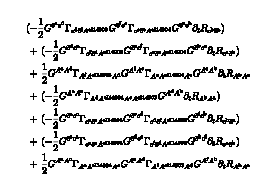

```mathematica
TakeDerivatives[Setup,WetterichEquation,
{A[p,{a,b}],A[-p,{a,b}]}
][[1]];
%//Truncate[Setup,#]&;
%//FPrint[Setup,#]&
```

```mathematica
ReduceIndices[setup_,term_FTerm]:=Module[
{closedSIndices,
cases,i,allObj,
subCase,subObj,subIndices,
subsubObj,
originalCases,result=term
},
(*TODO: TAKE CARE OF NESTED ENTRIES*)
closedSIndices=GetClosedSuperIndices[setup,term];

cases=Cases[term,γ[__],Infinity];
originalCases=cases;
cases[[All,1]]=Map[{{#[[1]]},{#[[2]]}}&,cases[[All,1]]];
cases[[All,2]]=Map[{{#[[1]]},{#[[2]]}}&,cases[[All,2]]];

(*The following code expands the γ[{f1,f2},{i1,i2}] into γ[{{f1,p[f1]},{f2,p[f2]}},{{i1,p[i1]},{i2,p[i2]}}], where the p[...] are the "partners", i.e. the matching indices somewhere else. If no partner exists, p[...]=0. This effectively marks open indices.*)
allObj=ExtractObjectsWithIndex[setup,term];
Do[
subIndices=Flatten[cases[[i,2,All]]]//.Times[-1,a_Symbol]:>a;
subObj=Select[allObj,(Or@@Table[MemberQ[#,subIndices[[j]],Infinity],{j,1,Length[subIndices]}])&];

Do[
subsubObj=Select[subObj,Head[#]=!=γ&&MemberQ[#,subIndices[[j]],Infinity]&];
If[Not[Length[subsubObj]<=1],Abort[]];

(*No partner exists*)
If[Not@MemberQ[closedSIndices,subIndices[[j]]],
AppendTo[cases[[i,1,j]],0];
AppendTo[cases[[i,2,j]],0];
Continue[]
];

(*Get the partner position*)
fIdx=FirstPosition[subsubObj[[1,2]]//.Times[-1,a_Symbol]:>a,subIndices[[j]]][[1]];
AppendTo[cases[[i,1,j]],subsubObj[[1,1,fIdx]]];
AppendTo[cases[[i,2,j]],-cases[[i,2,j,1]]];
,{j,1,Length[subIndices]}];

,{i,1,Length[cases]}];

(*Now, we use this information to reduce what we can*)
Do[
subCase=cases[[i]];

(*Let's start with the possible zero entries.*)
If[FreeQ[subCase[[1,1]],AnyField]&&
FreeQ[subCase[[1,1]],0]&&
subCase[[1,1,1]]=!=GetPartnerField[setup,subCase[[1,1,2]]],
result=result//.originalCases[[i]]:>0;
Continue[];
];
If[FreeQ[subCase[[1,2]],AnyField]&&
FreeQ[subCase[[1,2]],0]&&
subCase[[1,2,1]]=!=GetPartnerField[setup,subCase[[1,2,2]]],
result=result//.originalCases[[i]]:>0;
Continue[];
];
If[FreeQ[subCase[[1,All,1]],AnyField]&&
FreeQ[subCase[[1,All,1]],0]&&
subCase[[1,1,1]]=!=GetPartnerField[setup,subCase[[1,2,1]]],
result=result//.originalCases[[i]]:>0;
Continue[];
];

If[(Count[Flatten[subCase[[1]]],AnyField]+Count[Flatten[subCase[[1]]],0])===4,
Print["yet",subCase[[1]]]
];


If[Length[subCase[[1,1]]]===1&&Length[subCase[[1,2]]]===1,
Print["nope"];
Continue[]
];
repl={};
(*Then check the left index*)
If[Length[cases[[i,1,1]]]===2,
If[cases[[i,1,1,1]]===GetPartnerField[setup,cases[[i,1,1,2]]],
j
]
];
(*Then the right one*)
If[Length[cases[[i,1,2]]]===2,
If[cases[[i,1,2,1]]===GetPartnerField[setup,cases[[i,1,2,2]]],
Print["bye at ",cases[[i]]],

]
];
,{i,1,Length[cases]}
];

Print[cases];
Return[result];
];
ReduceIndices[setup_,eq_FEq]:=Module[{},
Map[ReduceIndices[setup,#]&,eq]
];
```